```mathematica
(* Eksplicitne enačbe *)
(* AB *)
x1[t1_]=x01+r0 Cos[t1];
y1[t1_]=y01+r0 Sin[t1];
(* BC *)
x2[t2_]=x02+r1 Cos[t2];
y2[t2_]=y02+r1 Sin[t2];
(* CD *)
x3[t3_]=x03+r2 Cos[t3];
y3[t3_]=y03+r2 Sin[t3];
(* DE *)
x4[t4_]=x04+t4 Sin[αkr];
y4[t4_]=y04-t4 Cos[αkr];
(* EF *)
x5[t5_]=x05+r3 Cos[t5];
y5[t5_]=y05+r3 Sin[t5];
(* FG *)
x6[t6_]=x06+r4 Cos[t6];
y6[t6_]=y06+r4 Sin[t6];
(* GH *)
x7[t7_]=x07+r5 Cos[t7];
y7[t7_]=y07+r5 Sin[t7];
```

{1.5708,1.82512,1.82512,2.81573,2.81573,3.66519,-1.33917,2.46711,3.66519,5.52735,-0.755836,-0.372368,-3.51396,-4.71239,4.07789,-24.8584,-2.31253,-0.275428,0.434862,-1.20378,-3.65869,-5.11354,-1.3859,-6.65012,-10.9188,2.33513,4.07789,-3.5224,28,2.6,5.5,1.2,14.3,1.8,0.523599}

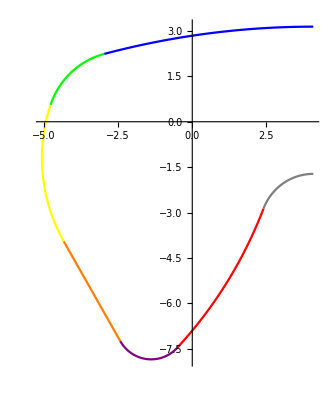

```mathematica
{t1A,t1B,t2B,t2C,t3C,t3D,t4D,t4E,t5E,t5F,t6F,t6G,t7G,t7H,x01,y01,x02,y02,x03,y03,x04,y04,x05,y05,x06,y06,x07,y07, r0, r1, r2, r3, r4, r5, αkr}=ReadList["C:\\Users\\Jure\\OneDrive\\fakulteta\\5.semester\\diplomska\\python\\clen_prenos.txt",Number]

Show[
ParametricPlot[{x1[t1], y1[t1]},{t1, t1A, t1B}, PlotStyle->Blue, PlotRange->All, AxesOrigin->{0,0} ],
ParametricPlot[{x2[t2], y2[t2]}, {t2, t2B,t2C}, PlotStyle->Green],
ParametricPlot[{x3[t3], y3[t3]}, {t3, t3C,t3D}, PlotStyle->Yellow],
ParametricPlot[{x4[t4], y4[t4]}, {t4, t4D,t4E}, PlotStyle->Orange],
ParametricPlot[{x5[t5], y5[t5]},{t5, t5E, t5F}, PlotStyle->Purple],
ParametricPlot[{x6[t6], y6[t6]}, {t6, t6F,t6G}, PlotStyle->Red],
ParametricPlot[{x7[t7], y7[t7]}, {t7, t7G,t7H}, PlotStyle->Gray],
AspectRatio->Full
]
```